# Normal Distribution with Exponential Survival Shifts Mean

## Laurens Bogaardt | RIVM | SIM | 2020

This document show that the distribution of survivors when the effect of a risk-factor on survival is exponentially increasing with the dose and the original population is normal, is also normal with a shifted mean.

## Visualisation

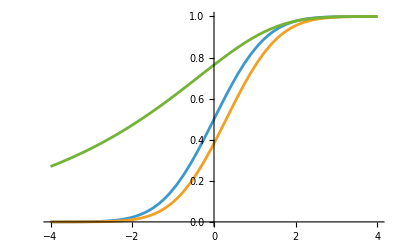

```mathematica
Plot[{1/2+1/2 Erf[x/Sqrt[2]],1/2+1/2 Erf[(x-0.3)/Sqrt[2]],(1+Erf[(x-0.3)/Sqrt[2]])/(1+Erf[x/Sqrt[2]])},{x,-4,4}]
```

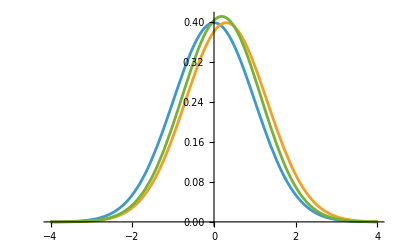

```mathematica
Plot[{PDF[NormalDistribution[],x],PDF[NormalDistribution[0.3,1],x],PDF[NormalDistribution[],x](1+Erf[(x-0.3)/Sqrt[2]])/(1+Erf[x/Sqrt[2]])/s},{x,-4,4}]
```

```mathematica
s=NIntegrate[PDF[NormalDistribution[],x](1+Erf[(x-0.3)/Sqrt[2]])/(1+Erf[x/Sqrt[2]]),{x,-4,4}]
```

0.754885

```mathematica
Integrate[PDF[NormalDistribution[0.3,1],x],x]
```

0.5 Erf[0.707107 (-0.3+1. x)]

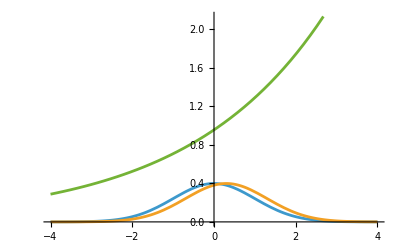

```mathematica
Plot[{PDF[NormalDistribution[],x],PDF[NormalDistribution[0.3,1],x],PDF[NormalDistribution[0.3,1],x]/PDF[NormalDistribution[],x]},{x,-4,4}]
```

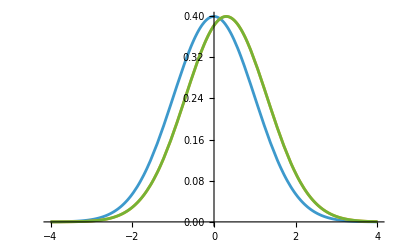

```mathematica
Plot[{PDF[NormalDistribution[],x],PDF[NormalDistribution[0.3,1],x],PDF[NormalDistribution[],x]PDF[NormalDistribution[0.3,1],x]/PDF[NormalDistribution[],x]},{x,-4,4}]
```

```mathematica
Simplify[PDF[NormalDistribution[0.3,1],x]/PDF[NormalDistribution[],x]]
```

0.955997 ⅇ^(0.3 x)

```mathematica
Simplify[PDF[NormalDistribution[m,1],x]/PDF[NormalDistribution[],x]]
```

ⅇ^(1/2 (x^2-(x-Function[{x},3.4-0.0001 (x-50)^2])^2))

```mathematica
biasedMean=Integrate[x PDF[NormalDistribution[mean,sd],x]Exp[-h x],{x,-Infinity,Infinity},Assumptions->{sd>0}]
```

ⅇ^(1/2 h (-2 mean+h sd^2)) (mean-h sd^2)

```mathematica
biasedSD=Integrate[(x-biasedMean)^2 PDF[NormalDistribution[mean,sd],x]Exp[-h x],{x,-Infinity,Infinity},Assumptions->{sd>0}]
```

ⅇ^(1/2 h (-6 mean+h sd^2)) (ⅇ^(h^2 sd^2) (mean-h sd^2)^2-2 ⅇ^(h mean+(h^2 sd^2)/2) (mean-h sd^2)^2+ⅇ^(2 h mean) (sd^2+(mean-h sd^2)^2))